# Loading Initial Results

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness α
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance m

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]](* So Mathematica knows the directory for our files *)
resX = 20; (* Incoming direction in [0,π/2[ *)
resY=10; (* Roughness in [0,1] *)
resZ=8;  (* Albedos in [0,1[ *)
rawFiles = Table[{i},{i,1,resZ}];
For[albedo=0,albedo<resZ,albedo++,{
str=OpenRead["results_order2_slice" <> ToString[albedo] <> ".bin",{BinaryFormat->True}];
rawFile = BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
rawFiles[[1+albedo]]= Table[Table[  rawFile[[1+resX*(j-1)+(i-1)]], {i,1,resX}],{j,1,resY}];
Close[str];
} ]
MatrixForm[rawFiles[[1]]];
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse\0) Fitting Flattening\Export

# Parametrization of Θ

```mathematica
paramsTheta = Table[ Table[rawFiles[[albedo]][[j]][[i]][[1]],{j,1,resY},{i,1,resX}],{albedo,1,resZ}];
MatrixForm[paramsTheta];
```

```mathematica
Show[Table[ListPlot3D[paramsTheta[[albedo]],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,π/2}}], {albedo,1,resZ}]]
```

-Graphics3D-

No surprise there : the diffuse lobe is almost static and has no prefered direction so θ = 0 ⟹ One less parameter to worry about!
NOTE: Now it’s completely flat because I really constrained the θ parameter to 0 in subsequent simulations.

# Parametrization of the Lobe’s Flattening Factor σ_n

```mathematica
paramsFlat = Table[Table[rawFiles[[albedo]][[j]][[i]][[4]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ ListPlot3D[paramsFlat[[1]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Red],
ListPlot3D[paramsFlat[[2]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Blue]]
ListPlot3D[paramsFlat[[3]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}];
ListPlot3D[paramsFlat[[4]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}];
```

-Graphics3D-

We see that for albedo 1 and 0.75, the shape is pretty similar (assuming precision errors for low roughness) and that for lower albedos the change was neglected and is always 1.
We thus concentrate on albedo 1 to fit what seems to be a pretty straightforward shape, except when roughness becomes low in which case the fitter resorted to the default value and modified the other parameters instead.
So basically our range of confidence in ρ is from index 1 to about 6.

{{0,0.670703},{1/19,0.67364},{2/19,0.675127},{3/19,0.697848},{4/19,0.6942},{5/19,0.647259},{6/19,0.552402},{7/19,0.621536},{8/19,0.802873},{9/19,0.593131},{10/19,0.702515},{11/19,0.699643},{12/19,0.702732},{13/19,0.702571},{14/19,0.702962},{15/19,0.702027},{16/19,0.699984},{17/19,0.707617},{18/19,0.795464},{1,0.576123}}

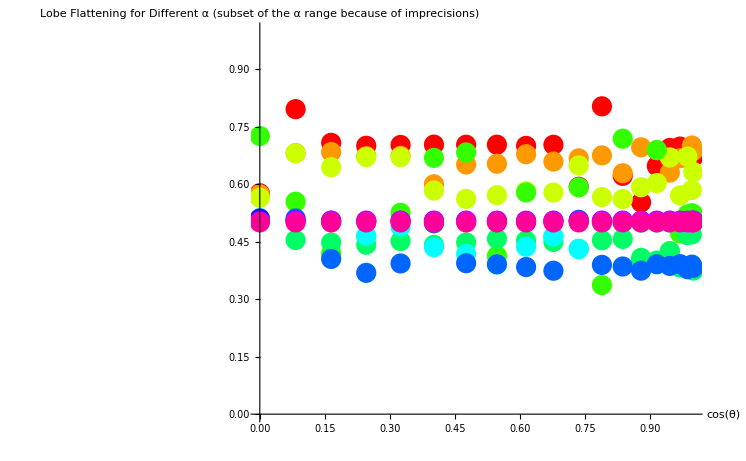

```mathematica
test=Table[{(i-1)/(resX-1),  paramsFlat[[1]][[1]][[i]]},{i,1,resX}]
ListPlot[test];
valuesSn=Table[Table[{Cos[(i-1)/(resX-1)*π/2],paramsFlat[[1]][[j]][[i]]},{i,1,resX}],{j,1,resY}];
Show[Table[ListPlot[valuesSn[[j]],PlotRange->{0,1} , PlotStyle->Hue[0.1*(j-1)],AxesLabel->{"cos(θ)","Lobe Flattening for Different α\n(subset of the α range because of imprecisions)"}],{j,1,resY}]]
```

Contrary to previous simulations with the incorrect histogram bin distribution, it appears that this time there is no more a dependency on cos(θ) but rather solely on roughness α...
We will try and average these values to obtain a single scale value for each roughness and then fit this with a function of roughness alone

```mathematica
linearFitsSn = Table[LinearModelFit[valuesSn[[j]],x,x],{j,1,resY}];
Plot[Table[linearFitsSn[[j]][x],{j,1,resY}],{x,0,1}];
```

{{1,0.681018},{8/9,0.661714},{7/9,0.610097},{2/3,0.534574},{5/9,0.440882},{4/9,0.477334},{1/3,0.409698},{2/9,0.504373},{1/9,0.504496},{0,0.5}}

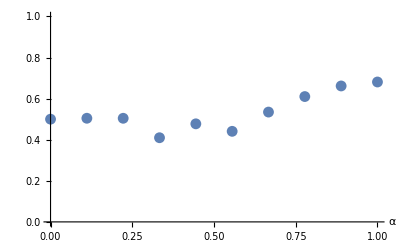

```mathematica
avgValuesSn = Table[{1-(j-1)/(resY-1),1/resX Sum[valuesSn[[j]][[i]][[2]],{i,1,resX}]},{j,1,resY}]
ListPlot[avgValuesSn,PlotRange->{0,1},AxesLabel->{"α"}]
```

0.5+c u^2

FindFit::lmnl: The model 0.5  + c\ u^2 is linear in the parameters {a, b, c}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

{a→1.,b→1.,c→0.153306}

(a→1.
b→1.
c→0.153306)

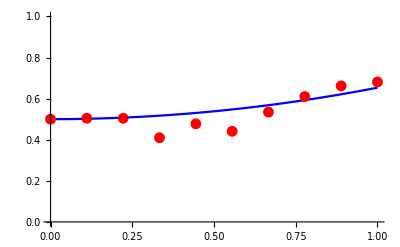

```mathematica
Clear[a,b,c,d,u]
modelSn=a+b*Exp[-c * u];
modelSn=a+b*Power[2,-c * u];
modelSn=0.5+0*b*u+c*u^2   (* Here we simply assume a 0.5 origin and ignore the linear term *)
fittingSn = FindFit[ avgValuesSn,modelSn,{a,b,c},u ,Method->"ConjugateGradient"]
MatrixForm[fittingSn]
Show[
Plot[modelSn/.fittingSn,{u,0,1},PlotRange->{0,1},PlotStyle->Blue],
ListPlot[avgValuesSn,PlotRange->{0,1} , PlotStyle->Red]
]
```

#### Final Expression

We can now obtain the final expression for the function matching the lobe flattening factor:

	f( α ) = 0.5 + 0.153306 α^2

```mathematica
N[c/.fittingSn[[3]]]
f[ μ_,α_] = 0.5+0.1533059468269667 α^2;
Plot3D[f[μ,α],{μ,0,1},{α,0,1},PlotRange->{0,1},AxesLabel->{"cos(θ)","α","Lobe Flattening"}]
```

0.153306

-Graphics3D-

#### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsFlat[[1]],PlotRange->{0,1},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[f[Cos[(i-1)/(resX-1)π/2],1-(j-1)/(resY-1)],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

Pretty good! 
Now we can remove that parameter from the simulation and use our fitting instead. That should help us stabilize the other parameters...

# Parametrization of the Lobe’s Masking Parameter m

```mathematica
paramsMasking = Table[Table[rawFiles[[albedo]][[j]][[i]][[5]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ ListPlot3D[paramsMasking[[1]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Red],
ListPlot3D[paramsMasking[[2]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Blue],
ListPlot3D[paramsMasking[[3]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}],
ListPlot3D[paramsMasking[[4]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}]]
```

-Graphics3D-

Without surprise, we can fix that parameter to 0 to avoid bumps in the scale parameter.

# Parametrization of the Lobe’s Roughness Parameter α

Here is our relation between roughness α and lobe exponent η:

```mathematica
roughness2exponent[α_] := 2^(10*(1-α))-1
roughness2exponent[0.95913]
```

0.327489

```mathematica
paramsRoughness = Table[Table[rawFiles[[albedo]][[j]][[i]][[2]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
paramsExponent = Table[Table[roughness2exponent[rawFiles[[albedo]][[j]][[i]][[2]]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ ListPlot3D[paramsRoughness[[1]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Red],
ListPlot3D[paramsRoughness[[2]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Blue]]
ListPlot3D[paramsRoughness[[3]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}];
ListPlot3D[paramsRoughness[[4]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}}];
```

-Graphics3D-

```mathematica
Show[ Table[ListPlot3D[paramsRoughness[[albedo]],{ PlotRange->{0.85,1.0},AxesLabel->{"θ","α"}},PlotStyle->Hue[albedo/(4*resZ)]],{albedo,1,resZ-4}]]
```

-Graphics3D-

### Representative Shape

It appears the lobe roughness is pretty much identical for different albedos so we could build an average plot:

```mathematica
avgParamsRoughness=1/4 Sum[paramsRoughness[[albedo]],{albedo,1,4}];
ListPlot3D[avgParamsRoughness,PlotRange->{0.85,1}]
```

Now, by averaging a few “roughness lines” in the middle of the surface, we can obtain an average plot of α as a function of surface’s α_s alone (we ignore the dependency on θ):

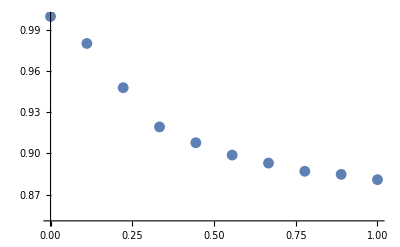

```mathematica
avgRoughness=Table[{1-(j-1)/(resY-1),1/16 Sum[avgParamsRoughness[[j]][[i]],{i,1,16}]},{j,1,resY}];
ListPlot[avgRoughness,PlotRange->{0.85,1}]
```

### Choosing the Model

```mathematica
Clear[a,b,c,d]
modelEta=0*a+b*u-c*u^2;
modelEta=0*a+b*u+c*u^2+d*u^3;
fittingEta = FindFit[ dataMaxExponent,{modelEta},{a,b,c,d},u ];
fEta[α_]=Evaluate[modelEta/.fittingEta/.u->α]
MatrixForm[fittingEta]
MatrixForm[modelEta/.fittingEta];
Show[
Plot[fEta[α],{α,0,1},PlotRange->{0,1.5},PlotStyle->Red,AxesLabel->{"α_s",}],
ListPlot[dataMaxExponent,PlotRange->{0,1.5} , PlotStyle->Blue,AxesLabel->{"α_s",}]
]
```

#### Modeling the exponents

```mathematica
Show[ Table[ListPlot3D[roughness2exponent[paramsRoughness[[albedo]]],{ PlotRange->{0,1.5},AxesLabel->{"θ","α"}},PlotStyle->Hue[albedo/(4*resZ)]],{albedo,1,resZ}]];
Show[
ListPlot3D[paramsExponent[[1]],{ PlotRange->{0,1.5},AxesLabel->{"θ","α"}},PlotStyle->Red],
ListPlot3D[paramsExponent[[2]],{ PlotRange->{0,1.5},AxesLabel->{"θ","α"}},PlotStyle->Blue],
ListPlot3D[paramsExponent[[3]],{ PlotRange->{0,1.5},AxesLabel->{"θ","α"}},PlotStyle->Green]
]
Show[
ListPlot3D[roughness2exponent[1/3 Sum[paramsRoughness[[i]],{i,1,3}]],{ PlotRange->{0,1.5},AxesLabel->{"θ","α"}},PlotStyle->Red],
ListPlot3D[1/3 Sum[paramsExponent[[i]],{i,1,3}],{ PlotRange->{0,1.5},AxesLabel->{"θ","α"}},PlotStyle->Blue]
]
```

-Graphics3D-

-Graphics3D-

### Representative Shape

There seems to be a nice model to fit for the exponent depending on the surface’s θ and roughness α_s.
First we will try and model the most obvious tendency of the surface: its curvy slope depending on roughness α_s.
For this, let’s use the slope at its maximum value when θ = 0°

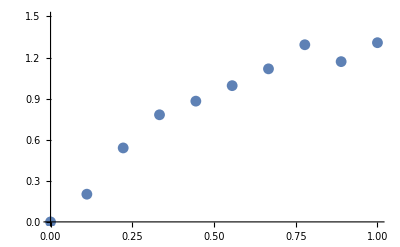

```mathematica
averageParamsExponent = 1/3 Sum[paramsExponent[[i]],{i,1,3}];
dataMaxExponent=Table[{1-(j-1)/(resY-1),averageParamsExponent[[j]][[1]]},{j,1,resY}];
ListPlot[dataMaxExponent,PlotRange->{0,1.5}]
```

### Choosing the Model

2.71026 α-1.69142 α^2+0.260868 α^3

(a→0.
b→2.71026
c→-1.69142
d→0.260868)

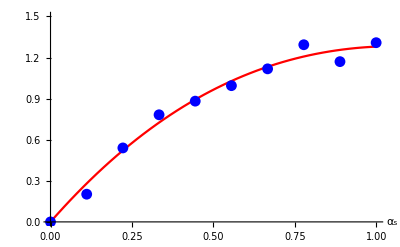

```mathematica
Clear[a,b,c,d]
modelEta=0*a+b*u-c*u^2;
modelEta=0*a+b*u+c*u^2+d*u^3;
fittingEta = FindFit[ dataMaxExponent,{modelEta},{a,b,c,d},u ];
fEta[α_]=Evaluate[modelEta/.fittingEta/.u->α]
MatrixForm[fittingEta]
MatrixForm[modelEta/.fittingEta];
Show[
Plot[fEta[α],{α,0,1},PlotRange->{0,1.5},PlotStyle->Red,AxesLabel->{"α_s",}],
ListPlot[dataMaxExponent,PlotRange->{0,1.5} , PlotStyle->Blue,AxesLabel->{"α_s",}]
]
```

```mathematica
NumberForm[N[b/.fittingEta[[2]]],16]
NumberForm[N[c/.fittingEta[[3]]],16]
NumberForm[N[d/.fittingEta[[4]]],16]
```

2.710256688555572

-1.691421934763379

0.2608681945033204

### Applying the Model

Now, let’s try and apply the model with different maximum amplitudes to try and match all the surface, this time depending on θ:

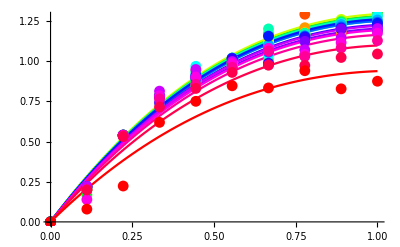

```mathematica
modelEta2=amp * fEta[α];
dataExponents=Table[Table[{1-(j-1)/(resY-1),averageParamsExponent[[j]][[i]]},{j,1,resY}],{i,1,resX}];

fittingAmp = Table[FindFit[ dataExponents[[i]],{modelEta2},{amp},α ],{i,1,resX}];
MatrixForm[fittingAmp];
Show[
Table[Plot[amp*fEta[α]/.fittingAmp[[i]],{α,0,1},PlotStyle->Hue[i/(1*resX)]],{i,1,resX}],
Table[ListPlot[dataExponents[[i]],PlotStyle->Hue[i/(1*resX)]],{i,1,resX}]
]
```

Fitting for all possible θ is okay-ish... Let’s see the amplitude as a function of cos(θ) now:

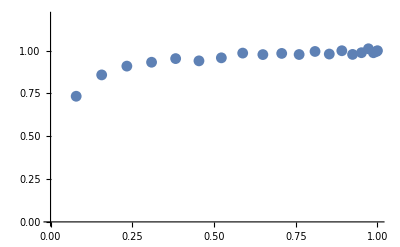

```mathematica
dataAmpCosTheta=Table[{Cos[(i-1)/resX*π/2],amp/.fittingAmp[[i]]},{i,1,resX}];
ListPlot[dataAmpCosTheta,PlotRange->{0,1.2}]
```

Here we have the choice to either fit amplitude as a function of cos(θ) or assume a constant amplitude of 1 all along and simply depend on α_s only...
I think the effort is quite futile since we’re after a simple model so let’s stick to the lobe roughness σ only being dependent on the surface roughness σ_s.

# Parametrization of the lobe’s Scale factor σ

```mathematica
paramsScale = Table[Table[rawFiles[[albedo]][[j]][[i]][[3]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ 
Table[ListPlot3D[paramsScale[[albedo]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->GrayLevel[1-albedo/resZ]],{albedo,1,resZ}]
]
```

-Graphics3D-

Still a lot of variations that can be attributed to variations in other parameters, especially masking and flattening. Now that we have appropriate analytical approximations for those, we can simply restart a simulation without them as free parameters and see what we get for the scale parameter then.